# The Half Cauchy distribution

This is code to accompany the book:
A Hitchhiker’s Guide to Multiple Scattering
© 2020 Eugene d’Eon 
http://www.eugenedeon.com/hitchhikers

## Definition

```mathematica
Cauchy`pc[s_]:=2/(Pi(1+s^2))
```

### normalization

```mathematica
Integrate[Cauchy`pc[s],{s,0,Infinity}]
```

1

### Mean and moments

The Cauchy distribution is heavy-tailed: it has an infinite moments of all orders.

```mathematica
Integrate[Cauchy`pc[s]s,{s,0,Infinity}]
```

∫_0^∞ (2 s)/(π (1+s^2))ⅆs

## GRT Statistics

```mathematica
Cauchy`Xc[s_]:=1-(2 ArcTan[s])/π
```

```mathematica
Cauchy`Σtc[s_]:=2/((1+s^2) (π-2 ArcTan[s]))
```

## Laplace Representation

```mathematica
LaplaceTransform[(2 Sin[q])/π,q,s]
```

2/(π (1+s^2))

## Laplace transform

```mathematica
FullSimplify[LaplaceTransform[Cauchy`pc[s],s,q],Assumptions->q>0]
```

(2 CosIntegral[q] Sin[q]+Cos[q] (π-2 SinIntegral[q]))/π

## Singular Eigenfunctions

```mathematica
c/2 Integrate[Exp[t u/v]Cauchy`pc[t],{t,0,Infinity},Assumptions->v>0&&-1<u<1]
```

ConditionalExpression[(c (-2 CosIntegral[-u/v] Sin[u/v]+Cos[u/v] (π+2 SinIntegral[u/v])))/(2 π),u≤0]

## Fourier Propagator

The dD Fourier propagator for the Cauchy distribution is

```mathematica
πd[d,Cauchy`pc[r]]
```

(2^(d/2) z^(1-d/2) Gamma[1+d/2] (BesselI[1/2 (-2+d),z]-StruveL[-1+d/2,z]))/d

## Grosjean F functions

```mathematica
pc=c Cauchy`pc[#]&
```

c Cauchy`pc[#1]&

```mathematica
Fpc[0,0,pc,z]
```

(c (1-Cosh[z]+Sinh[z]))/z

```mathematica
Fpc[1,0,pc,z]
```

(c MeijerG[{{1/2},{}},{{1/2,1/2},{-1}},z^2/4])/(2 √π)

```mathematica
Fpc[1,1,pc,z]
```

(c ⅇ^-z (-2+2 ⅇ^z-2 z-z^2))/z^3

```mathematica
Fpc[2,0,pc,z]
```

(c (-6+z^2+ⅇ^-z (6+2 z (3+z))))/(2 z^3)

```mathematica
Fpc[2,1,pc,z]
```

1/(4 √π z)c (z MeijerG[{{1/2},{}},{{1/2,1/2},{-1}},z^2/4]-z MeijerG[{{1/2},{}},{{1/2,3/2},{-2}},z^2/4]-MeijerG[{{1},{}},{{1,1},{-3/2}},z^2/4])

```mathematica
Fpc[2,2,pc,z]
```

(c ⅇ^-z (ⅇ^z (216-12 z^2+z^4)-4 (54+54 z+24 z^2+6 z^3+z^4)))/(4 z^5)

```mathematica
Fpc[l,0,pc,z]
```

2^(-2-l) c √π (2 z^l Hypergeometric0F1Regularized[3/2+l,z^2/4]-2^l z HypergeometricPFQRegularized[{1},{3/2-l/2,2+l/2},z^2/4]) Sec[(l π)/2]

## Random Variate Generation / Importance Sampling

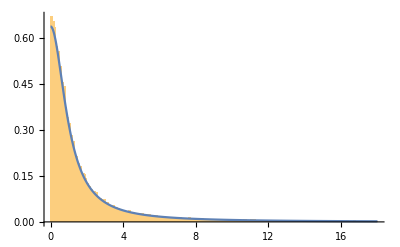

```mathematica
Show[
Histogram[Table[Tan[RandomReal[] Pi/2],{i,Range[100000]}],{0,18,0.1},"PDF"],
Plot[Cauchy`pc[x],{x,0,18},PlotRange->All]
]
```

## Full Cauchy distribution properties:

The ratio of two Normal random variables

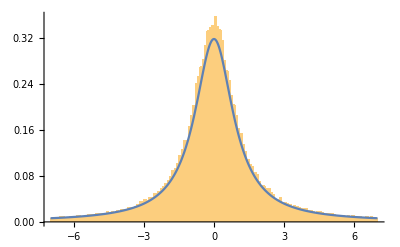

```mathematica
Show[
Histogram[Table[RandomVariate[NormalDistribution[]]/RandomVariate[NormalDistribution[]],{i,Range[100000]}],{-7,7,0.1},"PDF"],
Plot[1/2 Cauchy`pc[x],{x,-7,7}]
]
```